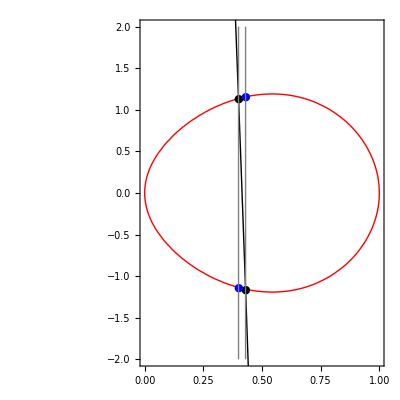

-1.98786

-1.7

{-0.532915}

{1.8885}

-1.8885

1.65583

```mathematica
Clear["Global`*"]
curveRHS=x^5-5x^3+4x; curve=curveRHS-y^2;

x1=-1.7 ; x2= -1.4; x3=0.4;x4=0.43;
y1=y/.NSolve[{curve==0,y<0,x==x1}][[1]];
y2=y/.NSolve[{curve==0,y>0,x==x2}][[1]];
y3=y/.NSolve[{curve==0,y>0,x==x3}][[1]];
y4=y/.NSolve[{curve==0,y<0,x==x4}][[1]];
P1={x1,y1};P2={x2,y2};P3={x3,y3};P4={x4,y4};
Y={y1,y2,y3,y4}; X={x1,x2,x3,x4};
A=Transpose [{X^3,X^2,X,{1,1,1,1}}];
{a,b,c,d}=LinearSolve[A,Y];
polynome=a*x^3+b*x^2+c*x+d;

x5=x/.NSolve[curveRHS==polynome^2][[5]];
x6=x/.NSolve[curveRHS==polynome^2][[6]];
y5=-y/.NSolve[{y==polynome,x==x5}][[1]];
y6=-y/.NSolve[{y==polynome,x==x6}][[1]];
P5={x5,y5};P6={x6,y6};

xmin=0;xmax=1 ;ymin=-2 ;ymax=2;
p1=ContourPlot[curve==0,{x,xmin,xmax},{y,ymin,ymax},ContourStyle->Red];
p2=Plot[polynome,{x,xmin,xmax},PlotStyle->Black];
p3=ListPlot[{P1,P2,P3,P4},PlotStyle->Black,PlotMarkers->{Automatic,Tiny}];
p4=ListPlot[{P5,P6},PlotStyle->Blue,PlotMarkers->{Automatic,Tiny}];
p5=ContourPlot[{x==x5,x==x6},{x,xmin,xmax},{y,ymin,ymax},ContourStyle->Gray];

Show[p1,p2,p3,p4,p5]
{{x5,y5},{x6,y6}};
xa=x/.NSolve[curveRHS==polynome^2][[1]]
xb=x/.NSolve[curveRHS==polynome^2][[3]]
ya=-y/.NSolve[{y==polynome,x==xa}];
yb=-y/.NSolve[{y==polynome,x==xb}];
ya
yb
y1
y2
```